# Clear console

```mathematica
Quiet@Remove["Global`*"]
SetDirectory[NotebookDirectory[]];
$MinPrecision=55*$MachinePrecision;
```

# Parameters

```mathematica
nmax=115;
var={u,v,w,z};
par={a,b};
nvar=Length[var];
fixedpar={α->1,β->1/2,δ->(21+√313)/48}//N;
parval={a->3,b->(841+37*√313)/128}//N;
ηval={ηNF->-0.0919995105221395}//N;
ξval={ξNF->-0.801397527511603}//N;
κval={κNF^2->ⅈ}//N;
C11eval={C11->0.109084591223343*ⅈ}//N;
A3eval={Subscript[ANF, 3]->0.145930074159533-0.00947358642130998*ⅈ}//N;
```

# Equation

```mathematica
kinetics={a-(b+1)*u+u^2*v+α*(w-u),b*u-u^2*v+β*(z-v),a-(b+1)*w+w^2*z+α*(u-w),b*w-w^2*z+β*(v-z)};
diffmatrix=({{δ^2, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, δ^2, 0}, {0, 0, 0, 1}});
eq=Solve[kinetics==0,var][[1]];
jacmat=D[kinetics,{var}]/.eq;
kinetics=kinetics/.Table[var[[varnum]]->var[[varnum]]+(var[[varnum]]/.eq),{varnum,nvar}];
```

# Kernel of the Jacobian matrix

```mathematica
dummymat=Table[Subscript[dmat, row,col],{row,nvar},{col,nvar}];
dummyvec=Table[Subscript[dvec, varnum],{varnum,nvar}];
jacobianmat=jacmat-μNF*diffmatrix/.fixedpar;
Tcond2=D[Det[jacobianmat],μNF];
μval=Solve[Tcond2==0,μNF][[3]]/.parval;
jacobianmat=jacobianmat;
ϕNF=Table[Subscript[vNF, varnum],{varnum,nvar}];
getout=0;
For[row=1,row<=nvar,row++,
If[getout==1,
Break[]];
For[col=1,col<=nvar,col++,
submatrixrows=Complement[Range[nvar],{row}];
submatrixcols=Complement[Range[nvar],{col}];
If[Det[jacobianmat[[submatrixrows,submatrixcols]]/.μval/.parval]!=0,
criticalrow=row;
criticalcol=col;
getout=1;
Break[];
]
];
]
ϕNF[[criticalcol]]=1;
ϕsol=Solve[Dot[jacobianmat[[submatrixrows,submatrixcols]],ϕNF[[submatrixcols]]]==-jacobianmat[[submatrixrows,{criticalcol}]],ϕNF[[submatrixcols]]][[1]];
ϕNF=ϕNF/.ϕsol;
Subscript[sol, 1,1]=Table[Subscript[WNF, 1,1,varnum]->C11*ϕNF[[varnum]],{varnum,nvar}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

# Kernel of the adjoint

```mathematica
ψNF=Table[Subscript[vNF, varnum],{varnum,nvar}];
ψNF[[criticalrow]]=1;
ψsol=Solve[Dot[Transpose[jacobianmat[[submatrixrows,submatrixcols]]],ψNF[[submatrixrows]]]==-Transpose[jacobianmat[[{criticalrow},submatrixcols]]],ψNF[[submatrixrows]]][[1]];
ψNF=ψNF/.ψsol/.fixedpar;
```

# Variables to expand

```mathematica
jacobianmat=jacobianmat/.parval;
jacobianmatr=jacmat-rNF^2*μNF*diffmatrix/.parval/.fixedpar;
ϕNF=ϕNF/.μval/.parval/.C11eval;
ψNF=ψNF/.μval/.parval;
Subscript[sol, 1,1]=Subscript[sol, 1,1]/.μval/.parval/.C11eval;
negativetab=Table[ⅇ^(ⅈ*subsub*x)->0,{subsub,-nmax,-1}];
positivetab=Table[ⅇ^(ⅈ*subsub*x)->0,{subsub,1,nmax}];
solr1=LinearSolve[dummymat[[submatrixrows,submatrixcols]],dummyvec[[submatrixcols]]];
solrn1=LinearSolve[dummymat,dummyvec];
toexpand=Flatten[Table[Subscript[var⟦varnum⟧, order]->Sum[Subscript[WNF, order,sub,varnum] ⅇ^(ⅈ sub x)/.Subscript[WNF, order,sub,varnum]->If[sub<0,(-1)^order*ⅇ^(2*sub*ξNF*π)*Conjugate[Subscript[WNF, order,-sub,varnum]]/.ξval,Subscript[WNF, order,sub,varnum]],{sub,-order,order,2}],{order,nmax},{varnum,nvar}]];
toexpand=toexpand/. Subscript[sol, 1,1];
expr=kinetics/.Table[var[[varnum]]->∑_(order=1)^nmax ϵNF^order*Subscript[var[[varnum]], order],{varnum,nvar}]/.parval/.fixedpar;
derivative=D[expr,ϵNF];
```

# Iterative solver

```mathematica
load=1;
If[FileExistsQ["savedSession.mx"] && load==1,
<<savedSession.mx
,
solvcond={};
ampeval={};
AppendTo[solvcond,0];
]
For[order=If[solvcond=={},2,Length[solvcond]+1],order<=nmax,order++,
save=0;
Print["order="<>ToString[order]];
derivative=D[derivative,ϵNF];
toexpand=toexpand/.ampeval;
equation=1/(order!)*derivative/.ϵNF->0/.toexpand;
equation=Expand[equation]/.negativetab;
If[OddQ[order],
sub=1;
auxeq=Chop[1/(2π)∫_0^(2π) equation*ⅇ^(-ⅈ*sub*x)ⅆx];
auxeq=-(auxeq-Dot[jacobianmatr/.rNF->0,Table[Subscript[WNF, order,sub,varnum],{varnum,nvar}]])//Simplify;
If[order>=3,
If[order-2>=sub && OddQ[order],
auxeq=auxeq-2*ⅈ*sub*(order-2-2*ⅈ*sub*ηNF)/2*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-2,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-2,sub]/.ηval;
]
];
If[order>=5,
If[order-4>=sub && OddQ[order],
auxeq=auxeq-((order-2-2*ⅈ*sub*ηNF)*(order-4-2*ⅈ*sub*ηNF))/4*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-4,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-4,sub]/.ηval;
]
];
auxeq=auxeq/.fixedpar/.ampeval;
AppendTo[solvcond,Chop[Dot[auxeq,ψNF]/.μval/.fixedpar]//Simplify];
If[order>=7 && OddQ[order],
If[order==7,
partialsol=A3eval;
,
actualeq=solvcond[[order]];
partialsol=Quiet@NSolve[actualeq==0/.Subscript[ANF, order-2]->0,Subscript[ANF, order-4],Complexes][[1]];
];
ampeval=Join[ampeval,partialsol];
];
auxeq=auxeq/.ampeval;
usefulvec=Table[Subscript[auxvec, order,sub,varnum],{varnum,nvar}];
If[order==7,
auxsol=solr1/.Flatten[Table[dummymat[[row,col]]->jacobianmat[[row,col]],{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]]-(solvcond[[order]]/.Subscript[ANF, 5]->0)*ψNF[[varnum]]/Norm[ψNF]^2/.partialsol,{varnum,nvar}];
,
If[order==5,
auxsol=solr1/.Flatten[Table[dummymat[[row,col]]->jacobianmat[[row,col]],{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]]-(solvcond[[order]]/.Subscript[ANF, 3]->0)*ψNF[[varnum]]/Norm[ψNF]^2,{varnum,nvar}];
,
auxsol=solr1/.Flatten[Table[dummymat[[row,col]]->jacobianmat[[row,col]],{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]],{varnum,nvar}];
]
];
usefulvec[[submatrixcols]]=Table[Subscript[WNF, order,sub,submatrixcols[[varnum]]]->auxsol[[varnum]]+Subscript[ANF, order]*ϕNF[[submatrixcols[[varnum]]]],{varnum,nvar-1}];
usefulvec[[criticalcol]]=Subscript[WNF, order,sub,criticalcol]->Subscript[ANF, order]*ϕNF[[criticalcol]];
Subscript[sol, order,sub]=Chop[usefulvec]/.μval/.C11eval//Expand;
toexpand=toexpand/. Subscript[sol, order,sub];
,
AppendTo[solvcond,0];
];
For[sub=If[EvenQ[order],0,3],sub<=order,sub+=2,
save=1;
If[sub==0,
auxeq=equation/.positivetab;
,
auxeq=equation/.ⅇ^(ⅈ*sub*x)->1/.positivetab;
];
auxeq=-(auxeq-Dot[jacobianmatr/.rNF->0,Table[Subscript[WNF, order,sub,varnum],{varnum,nvar}]])//Simplify;
If[order>=3,
If[order-2>=Abs[sub] && ((OddQ[order] && OddQ[sub]) || (EvenQ[order] && EvenQ[sub])),
auxeq=auxeq-2*ⅈ*sub*(order-2-2*ⅈ*sub*ηNF)/2*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-2,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-2,sub]/.ηval;
]
];
If[order>=5,
If[order-4>=Abs[sub] && ((OddQ[order] && OddQ[sub]) || (EvenQ[order] && EvenQ[sub])),
auxeq=auxeq-((order-2-2*ⅈ*sub*ηNF)*(order-4-2*ⅈ*sub*ηNF))/4*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-4,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-4,sub]/.ηval;
]
];
auxeq=auxeq/.fixedpar/.ampeval;
auxsol=solrn1/.Flatten[Table[dummymat[[row,col]]->jacobianmatr[[row,col]]/.rNF->sub,{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]],{varnum,nvar}]/.μval/.C11eval;
Subscript[sol, order,sub]=Chop[Table[Subscript[WNF, order,sub,varnum]->auxsol[[varnum]],{varnum,nvar}]]/.ampeval//Expand;
toexpand=toexpand/. Subscript[sol, order,sub];
If[sub==0,
equation=equation-(Expand[equation]/.positivetab);
]
];
If[save==1 && sub==order+2,
DumpSave["savedSession.mx",{"Global`","Subscript"}]
]
]
```

order=2

order=3

order=4

order=5

order=6

order=7

order=8

order=9

order=10

order=11

order=12

order=13

order=14

order=15

order=16

order=17

order=18

order=19

order=20

order=21

order=22

order=23

order=24

order=25

order=26

order=27

order=28

order=29

order=30

order=31

order=32

order=33

order=34

order=35

order=36

order=37

order=38

order=39

order=40

order=41

order=42

order=43

order=44

order=45

order=46

order=47

order=48

order=49

order=50

order=51

order=52

order=53

order=54

order=55

order=56

order=57

order=58

order=59

order=60

order=61

order=62

order=63

order=64

order=65

order=66

order=67

order=68

order=69

order=70

order=71

order=72

order=73

order=74

order=75

order=76

order=77

order=78

order=79

order=80

order=81

order=82

order=83

order=84

order=85

order=86

order=87

order=88

order=89

order=90

order=91

order=92

order=93

order=94

order=95

order=96

order=97

order=98

order=99

order=100

order=101

order=102

order=103

order=104

order=105

order=106

order=107

order=108

order=109

order=110

order=111

order=112

order=113

order=114

order=115

# Tabulating information

```mathematica
SetDirectory[NotebookDirectory[]];
<<savedSession.mx
PrependTo[ampeval,Subscript[ANF, 1]->C11/.C11eval];
c00tabaux=Table[1/Dot[ϕNF,ϕNF]*((κNF^2/.κval)^(-(order-1)/2)*Dot[Table[Subscript[WNF, order,0,varnum],{varnum,nvar}]/. Subscript[sol, order,0],ϕNF]/.ampeval)/Gamma[(order-1)/2+3-ηNF*ⅈ]/.ηval/.C11eval,{order,2,Length[solvcond]-4,2}];
c20tabaux=Table[1/Dot[ϕNF,ϕNF]*((κNF^2/.κval)^(-(order-1)/2)*Dot[Table[Subscript[WNF, order,2,varnum],{varnum,nvar}]/. Subscript[sol, order,2],ϕNF]/.ampeval)/Gamma[(order-1)/2+3-ηNF*ⅈ]/.ηval/.C11eval,{order,2,Length[solvcond]-4,2}];
c00tab=Table[{Abs[c00tabaux[[ind]]],Arg[c00tabaux[[ind]]]},{ind,Length[c00tabaux]}];
c00tab[[All,1]]
c20tab=Table[{Abs[c20tabaux[[ind]]],Arg[c20tabaux[[ind]]]},{ind,Length[c20tabaux]}];
c20tab[[All,1]]
```

{0.0986261,0.0244341,0.0985067,0.0641368,0.0476713,0.0919457,0.0372236,0.100186,0.036043,0.102467,0.0371719,0.102357,0.0386189,0.101084,0.0398803,0.0991756,0.04086,0.0969046,0.0415693,0.0944225,0.0420471,0.0918186,0.0423337,0.0891442,0.0424674,0.0864318,0.0424799,0.0836992,0.042401,0.0809606,0.0422532,0.0782211,0.0420605,0.0754902,0.041837,0.072767,0.041605,0.0700626,0.0413695,0.06737,0.0411559,0.0647074,0.0409559,0.0620576,0.0408065,0.0594524,0.0406764,0.0568592,0.0406273,0.0543264,0.0405919,0.0518126,0.0406662,0.0493512,0.040756}

{0.000957982,0.000198156,0.000279232,0.000352464,0.000284747,0.000302447,0.000273055,0.000278022,0.000261716,0.000262403,0.000251319,0.000250119,0.000241564,0.000239392,0.000232387,0.00022974,0.000223889,0.00022099,0.000216076,0.000213136,0.000209084,0.000206159,0.000202841,0.000200087,0.000197566,0.000194969,0.000193033,0.000190747,0.000189676,0.00018768,0.000186949,0.000185309,0.000185728,0.000184652,0.000184879,0.000183845,0.000185936,0.000186397,0.000187177,0.000186045,0.000190109,0.000193753,0.000194727,0.000190822,0.000196695,0.00020827,0.000210724,0.000196163,0.000199782,0.000232493,0.000246211,0.00020274,0.00017989,0.000270232,0.000334469}

# Plotting

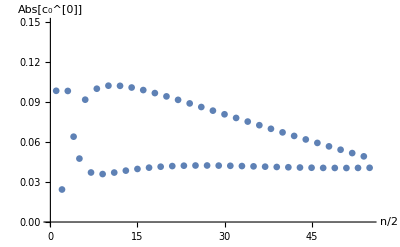

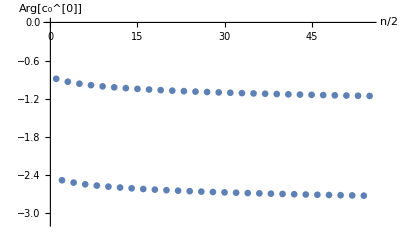

```mathematica
ps=0.012;
c00tabplotabs=ListPlot[Table[{n,c00tab[[n,1]]},{n,Length[c00tab]}],PlotRange->{{0,Length[c00tab]},{0.0,0.15}},AxesLabel->{"n/2","Abs[c_0^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
c00tabplotangle=ListPlot[Table[{n,c00tab[[n,2]]},{n,Length[c00tab]}],PlotRange->{{0,Length[c00tab]},{-π,0}},AxesLabel->{"n/2","Arg[c_0^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
```

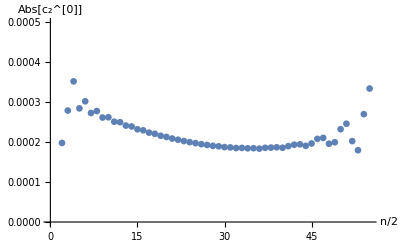

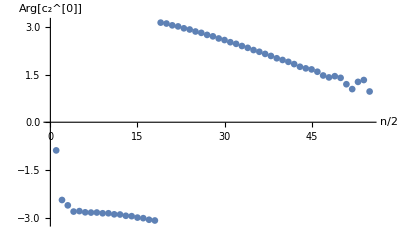

```mathematica
c20tabplotabs=ListPlot[Table[{n,c20tab[[n,1]]},{n,Length[c20tab]}],PlotRange->{{0,Length[c20tab]},{0.0,0.0005}},AxesLabel->{"n/2","Abs[c_2^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
c20tabplotangle=ListPlot[Table[{n,c20tab[[n,2]]},{n,Length[c20tab]}],PlotRange->{{0,Length[c20tab]},{-π,π}},AxesLabel->{"n/2","Arg[c_2^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
```

{param_0→-0.036216,param_1→3.02435,param_2→-19.0622}

{param_0→0.0380283,param_1→0.0645971,param_2→0.0400057}

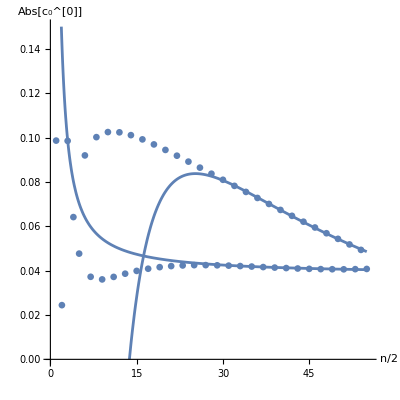

```mathematica
c00funabs=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c00tab[[2*n,1]]},{n,15,Floor[Length[c00tab]/2]}],c00funabs,parameters,n]
fitplot1=Plot[c00funabs/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{0,0.15}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
fitpar=FindFit[Table[{n,c00tab[[2*n-1,1]]},{n,15,Floor[Length[c00tab]/2]}],c00funabs,parameters,n]
fitplot2=Plot[c00funabs/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{0,0.15}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot1,fitplot2,c00tabplotabs,AxesLabel->{"n/2","Abs[c_0^[0]]"}]
```

{param_0→-2.83445,param_1→3.58615,param_2→-17.9743}

{param_0→-1.26365,param_1→3.63196,param_2→-18.0051}

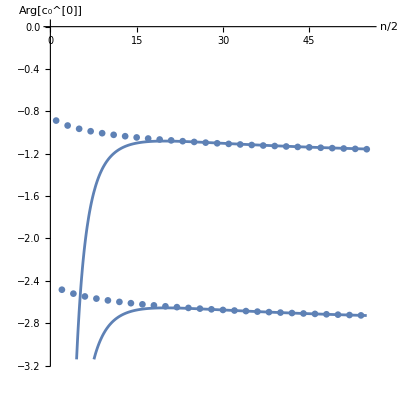

```mathematica
c00funangle=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c00tab[[2*n,2]]},{n,15,Length[c00tab]/2}],c00funangle,parameters,n]
fitplot1=Plot[c00funangle/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{-π,0}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
fitpar=FindFit[Table[{n,c00tab[[2*n-1,2]]},{n,15,Length[c00tab]/2}],c00funangle,parameters,n]
fitplot2=Plot[c00funangle/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{-π,0}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot1,fitplot2,c00tabplotangle,AxesLabel->{"n/2","Arg[c_0^[0]]"}]
```

{param_0→0.000315847,param_1→-0.00668021,param_2→0.086949}

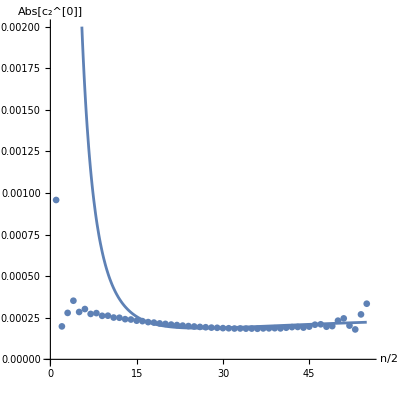

```mathematica
c20funabs=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c20tab[[n,1]]},{n,15,Length[c20tab]}],c00funabs,parameters,n]
fitplot=Plot[c20funabs/.fitpar,{n,0,Length[c20tab]},PlotRange->{{0,Length[c20tab]+0.5},{0.0,0.002}},AxesLabel->{"n/2","Abs[c_2^[0]]"},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot,c20tabplotabs]
```

{param_0→-2.87554,param_1→281.463,param_2→-3535.32}

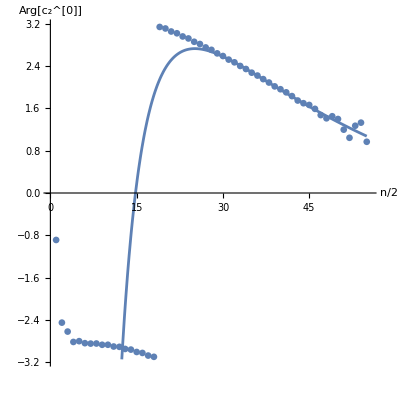

```mathematica
c20funangle=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c20tab[[n,2]]},{n,30,Length[c20tab]}],c00funangle,parameters,n]
fitplot=Plot[c20funangle/.fitpar,{n,0,Length[c20tab]},PlotRange->{{0,Length[c20tab]+0.5},{-π,π}},AxesLabel->{"n/2","Arg[c_2^[0]]"},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot,c20tabplotangle]
```